# Pullbacks and Pushforwards

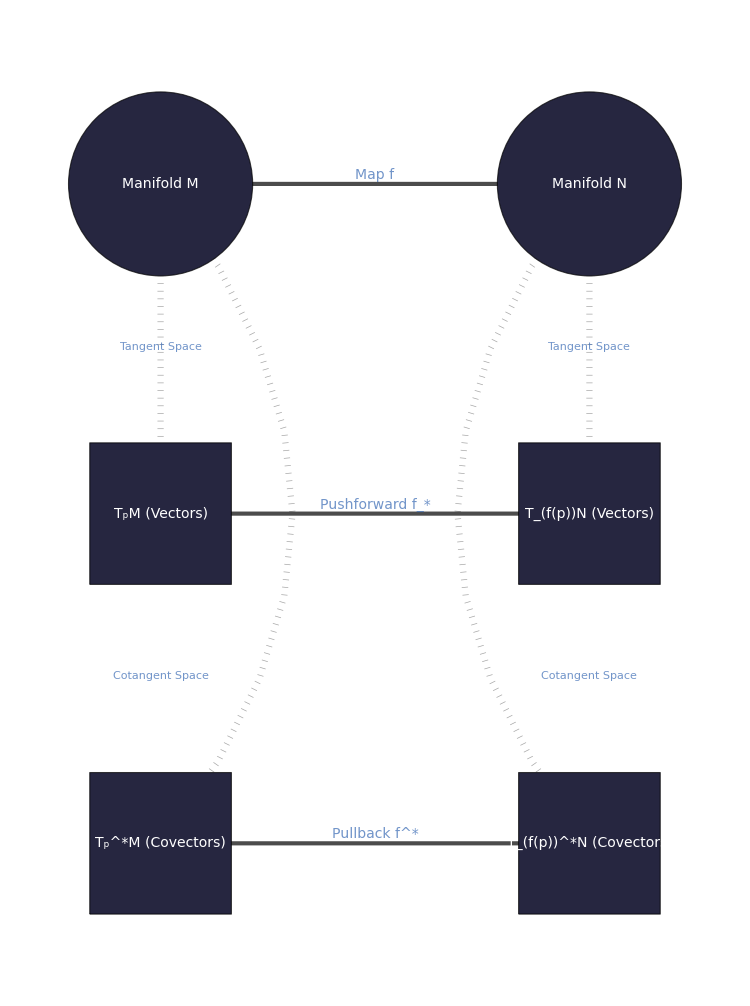

```mathematica
ClearAll[geomGraph];

With[{(*Helper function to style the structural labels with a white background*)strucLabel=Function[text,Framed[Style[text,12,GrayLevel[0.4],Bold],FrameStyle->None,Background->White,FrameMargins->2]]},geomGraph=Graph[{"M","N","TpM","TfN","TpMco","TfNco"},{(*Mathematical Maps*)DirectedEdge["M","N"],DirectedEdge["TpM","TfN"],DirectedEdge["TfNco","TpMco"],(*Structural Associations*)DirectedEdge["M","TpM"],DirectedEdge["M","TpMco"],DirectedEdge["N","TfN"],DirectedEdge["N","TfNco"]},VertexCoordinates->{"M"->{0,2},"N"->{1.3,2},"TpM"->{0,1},"TfN"->{1.3,1},"TpMco"->{0,0},"TfNco"->{1.3,0}},VertexLabels->{"M"->Placed["Manifold M",Center],"N"->Placed["Manifold N",Center],"TpM"->Placed["\!\(\*SubscriptBox[\(T\), \(p\)]\)M (Vectors)",Center],"TfN"->Placed["\!\(\*SubscriptBox[\(T\), \(f(p)\)]\)N (Vectors)",Center],"TpMco"->Placed["\!\(\*SubsuperscriptBox[\(T\), \(p\), \(*\)]\)M (Covectors)",Center],"TfNco"->Placed["\!\(\*SubsuperscriptBox[\(T\), \(f(p)\), \(*\)]\)N (Covectors)",Center]},EdgeLabels->{(*Main map labels lifted safely above the arrows*)DirectedEdge["M","N"]->Placed[Style["Map f",14],{0.5,{0.5,-0.2}}],DirectedEdge["TpM","TfN"]->Placed[Style["Pushforward \!\(\*SubscriptBox[\(f\), \(*\)]\)",14],{0.5,{0.5,-0.2}}],DirectedEdge["TfNco","TpMco"]->Placed[Style["Pullback \!\(\*SuperscriptBox[\(f\), \(*\)]\)",14],{0.5,{0.5,-0.2}}],(*Using {0.5,{0.5,0.5}} locks the absolute center of the text box precisely onto the line stroke*)DirectedEdge["M","TpM"]->Placed[strucLabel["Tangent Space"],{0.5,{0.5,0.5}}],DirectedEdge["N","TfN"]->Placed[strucLabel["Tangent Space"],{0.5,{0.5,0.5}}],(*{0.75,{0.5,0.5}} slides it down the curve,keeping the text dead-center over the dots*)DirectedEdge["M","TpMco"]->Placed[strucLabel["Cotangent Space"],{0.75,{0.5,0.5}}],DirectedEdge["N","TfNco"]->Placed[strucLabel["Cotangent Space"],{0.75,{0.5,0.5}}]},EdgeShapeFunction->{(*Draw the sweeping curves*)DirectedEdge["M","TpMco"]->GraphElementData[{"CurvedArc","Curvature"->0.8}],DirectedEdge["N","TfNco"]->GraphElementData[{"CurvedArc","Curvature"->-0.8}],(*EXPLICITLY lock the arrowheads on the main maps so the engine cannot delete them*)DirectedEdge["M","N"]->GraphElementData[{"FilledArrow","ArrowSize"->0.04}],DirectedEdge["TpM","TfN"]->GraphElementData[{"FilledArrow","ArrowSize"->0.04}],DirectedEdge["TfNco","TpMco"]->GraphElementData[{"FilledArrow","ArrowSize"->0.04}]},VertexShapeFunction->Function[{coord,name,size},If[name==="M"||name==="N",{RGBColor[0.15,0.15,0.25],Disk[coord,Max[size]*1.3]},{RGBColor[0.15,0.15,0.25],Rectangle[coord-size,coord+size]}]],VertexSize->{"Scaled",0.18},VertexLabelStyle->Directive[White,FontFamily->"Helvetica",14],EdgeStyle->{_->Directive[Black,AbsoluteThickness[3]],(*Re-apply the thick dotted style.Arrowheads[0] removes directional points from structural lines*)DirectedEdge["M","TpM"]->Directive[Dotted,GrayLevel[0.5],AbsoluteThickness[4.5],Arrowheads[0]],DirectedEdge["M","TpMco"]->Directive[Dotted,GrayLevel[0.5],AbsoluteThickness[4.5],Arrowheads[0]],DirectedEdge["N","TfN"]->Directive[Dotted,GrayLevel[0.5],AbsoluteThickness[4.5],Arrowheads[0]],DirectedEdge["N","TfNco"]->Directive[Dotted,GrayLevel[0.5],AbsoluteThickness[4.5],Arrowheads[0]]},ImagePadding->60,ImageSize->750]]
```

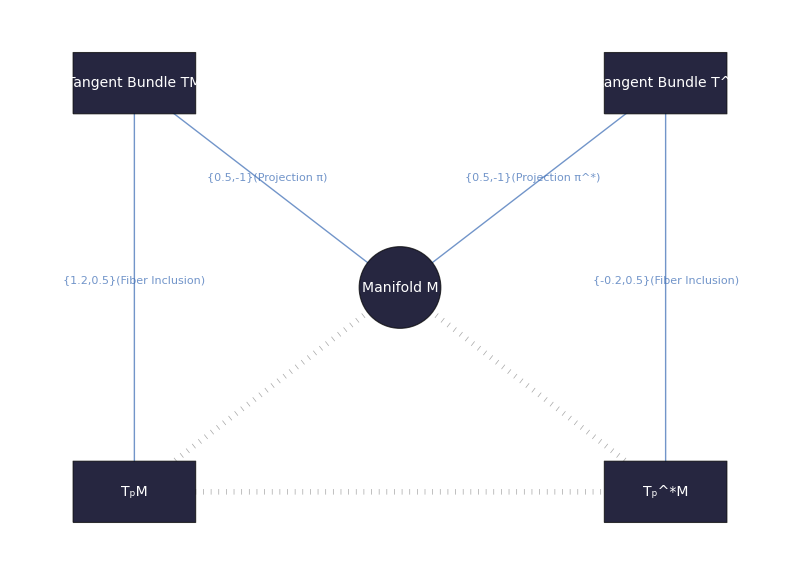

```mathematica
ClearAll[bundleGraph];

With[{(*White-background labels for structural lines*)strucLabel=Function[text,Framed[Style[text,12,GrayLevel[0.4],Bold],FrameStyle->None,Background->White,FrameMargins->2]],mapLabel=Function[text,Style[text,13,Black,Bold]]},bundleGraph=Graph[{"TM","TStarM","M","TpM","TpStarM"},{(*Projections*)DirectedEdge["TM","M"],DirectedEdge["TStarM","M"],(*Inclusions*)DirectedEdge["TpM","TM"],DirectedEdge["TpStarM","TStarM"],(*Associations (Base point attachment)*)DirectedEdge["M","TpM"],DirectedEdge["M","TpStarM"],(*Duality*)DirectedEdge["TpM","TpStarM"]},VertexCoordinates->{"TM"->{0,2},"TStarM"->{2.6,2},"M"->{1.3,1},"TpM"->{0,0},"TpStarM"->{2.6,0}},VertexLabels->{"TM"->Placed[Style["Tangent Bundle TM",14,White],Center],"TStarM"->Placed[Style["Cotangent Bundle \!\(\*SuperscriptBox[\(T\), \(*\)]\)M",14,White],Center],"M"->Placed[Style["Manifold M",14,White],Center],"TpM"->Placed[Style["\!\(\*SubscriptBox[\(T\), \(p\)]\)M",14,White],Center],"TpStarM"->Placed[Style["\!\(\*SubsuperscriptBox[\(T\), \(p\), \(*\)]\)M",14,White],Center]},EdgeShapeFunction->{(*Projections and Inclusions get Solid Arrows*)DirectedEdge["TM","M"]|DirectedEdge["TStarM","M"]|DirectedEdge["TpM","TM"]|DirectedEdge["TpStarM","TStarM"]->GraphElementData[{"FilledArrow","ArrowSize"->0.035}],(*Associations get Dotted Lines*)DirectedEdge["M","TpM"]|DirectedEdge["M","TpStarM"]|DirectedEdge["TpM","TpStarM"]->({Dotted,AbsoluteThickness[4],GrayLevel[0.5],Line[#1]}&)},EdgeLabels->{DirectedEdge["TM","M"]->Placed[mapLabel["Projection π"],0.5,{0.5,-1}],DirectedEdge["TStarM","M"]->Placed[mapLabel["Projection \!\(\*SuperscriptBox[\(π\), \(*\)]\)"],0.5,{0.5,-1}],DirectedEdge["TpM","TM"]->Placed[mapLabel["Fiber Inclusion"],0.5,{1.2,0.5}],DirectedEdge["TpStarM","TStarM"]->Placed[mapLabel["Fiber Inclusion"],0.5,{-0.2,0.5}],DirectedEdge["M","TpM"]->Placed[strucLabel["Attached at p"],{0.5,Center}],DirectedEdge["M","TpStarM"]->Placed[strucLabel["Attached at p"],{0.5,Center}],DirectedEdge["TpM","TpStarM"]->Placed[strucLabel["Dual Pairing"],{0.5,Center}]},VertexShapeFunction->Function[{coord,name,size},{RGBColor[0.15,0.15,0.25],If[name==="M",Disk[coord,0.2],Rectangle[coord-{0.3,0.15},coord+{0.3,0.15}]]}],ImagePadding->80,ImageSize->800]]
```

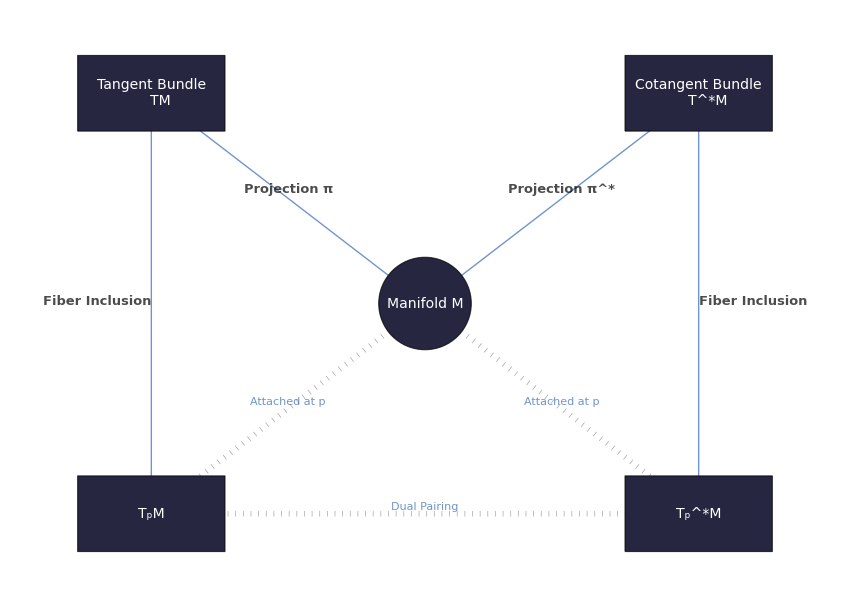

```mathematica
ClearAll[bundleGraph];

With[{(*White-background labels for structural lines to ensure legibility*)strucLabel=Function[text,Framed[Style[text,12,GrayLevel[0.4],Bold],FrameStyle->None,Background->White,FrameMargins->2]],(*Map labels without the coordinate spillover*)mapLabel=Function[text,Style[text,13,Black,Bold]]},bundleGraph=Graph[{"TM","TStarM","M","TpM","TpStarM"},{DirectedEdge["TM","M"],DirectedEdge["TStarM","M"],DirectedEdge["TpM","TM"],DirectedEdge["TpStarM","TStarM"],DirectedEdge["M","TpM"],DirectedEdge["M","TpStarM"],DirectedEdge["TpM","TpStarM"]},VertexCoordinates->{"TM"->{0,2},"TStarM"->{2.6,2},"M"->{1.3,1},"TpM"->{0,0},"TpStarM"->{2.6,0}},VertexLabels->{"TM"->Placed[Style["Tangent Bundle\n    TM",14,White],Center],"TStarM"->Placed[Style["Cotangent Bundle\n    \!\(\*SuperscriptBox[\(T\), \(*\)]\)M",14,White],Center],"M"->Placed[Style["Manifold M",14,White],Center],"TpM"->Placed[Style["\!\(\*SubscriptBox[\(T\), \(p\)]\)M",14,White],Center],"TpStarM"->Placed[Style["\!\(\*SubsuperscriptBox[\(T\), \(p\), \(*\)]\)M",14,White],Center]},EdgeLabels->{(*Standard Placed[label,pos] syntax to prevent coordinate printing*)DirectedEdge["TM","M"]->Placed[mapLabel["Projection π"],0.5],DirectedEdge["TStarM","M"]->Placed[mapLabel["Projection \!\(\*SuperscriptBox[\(π\), \(*\)]\)"],0.5],(*Using {0.5,{1.5,0.5}} to push the text horizontally away from the line*)DirectedEdge["TpM","TM"]->Placed[mapLabel["Fiber Inclusion"],{0.5,{1.5,0.5}}],DirectedEdge["TpStarM","TStarM"]->Placed[mapLabel["Fiber Inclusion"],{0.5,{-0.5,0.5}}],DirectedEdge["M","TpM"]->Placed[strucLabel["Attached at p"],0.5],DirectedEdge["M","TpStarM"]->Placed[strucLabel["Attached at p"],0.5],DirectedEdge["TpM","TpStarM"]->Placed[strucLabel["Dual Pairing"],0.5]},EdgeShapeFunction->{DirectedEdge["TM","M"]|DirectedEdge["TStarM","M"]|DirectedEdge["TpM","TM"]|DirectedEdge["TpStarM","TStarM"]->GraphElementData[{"FilledArrow","ArrowSize"->0.035}],DirectedEdge["M","TpM"]|DirectedEdge["M","TpStarM"]|DirectedEdge["TpM","TpStarM"]->({Dotted,AbsoluteThickness[4],GrayLevel[0.5],Line[#1]}&)},VertexShapeFunction->Function[{coord,name,size},{RGBColor[0.15,0.15,0.25],If[name==="M",Disk[coord,0.22],Rectangle[coord-{0.35,0.18},coord+{0.35,0.18}]]}],ImagePadding->100,ImageSize->850]]
```